1.

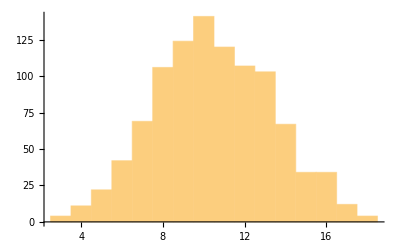

```mathematica
addDiceList = Table[Total[RandomInteger[{1,6},3]],1000];
Histogram[addDiceList]
```

2.

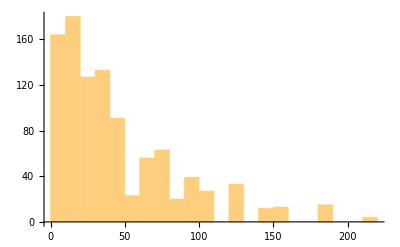

```mathematica
multiDiceList = Table[Product[RandomInteger[{1,6}],{i,1,3}],1000];
Histogram[multiDiceList]
```

3.

```mathematica
probSumIs10 = Length[Select[Table[Total[RandomInteger[{1,6},3]],10^8],#==10&]]/10^8;
N[probSumIs10,2]
```

0.13

4.

```mathematica
bigThree = Total[Table[Max[RandomInteger[{1,10},3]],10^6]/10^6]//N
```

7.97566

5.

```mathematica
midlleThree = Total[Table[Median[RandomInteger[{1,10},3]],10^6]/10^6]//N
```

5.49948

6.

```mathematica
probDistinct = Length[Select[Table[Length[DeleteDuplicates[RandomInteger[{1,100},40]]],10^6],#==31||30&]]/10^6;
N[probDistinct,2]
```

0.11